```mathematica
f[s_,k_,t_]:=FinancialDerivative[{"European","Call"}, {"StrikePrice"->k, "Expiration"->t},  {"InterestRate"-> 0, "Volatility" -> 0.5, "CurrentPrice"-> s, "Dividend"->0}]
```

```mathematica
s[x_,t_]:=x*f[1,2-1/x,t]+x-1;l[x_,t_]:=x*f[1,1/x,t];
```

Plot::exclul: {(1 - x - x\ FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}] + x\ FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}]) - 0, (-1 + x + x\ « 1 » - x\ FinancialDerivative[« 1 »]) - 0} must be a list of equalities or real-valued functions.

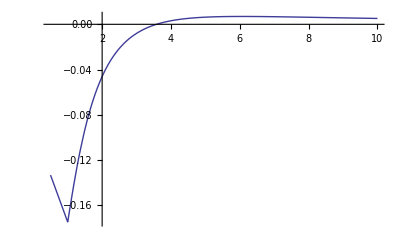

```mathematica
t=2;Plot[{-(x*0.0831607633153908+0.09171516666280866)+(l[x,t]+s[x,t])/2 0+Max[s[x,t],l[x,t]]-l[x,t]},{x,0.5005,10},PlotRange->All]
```

Plot::exclul: {(1 - x - x\ FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}] + x\ FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}]) - 0, (-1 + x + x\ « 1 » - x\ FinancialDerivative[« 1 »]) - 0} must be a list of equalities or real-valued functions.

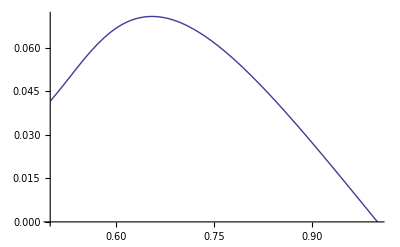

```mathematica
a=0;Plot[{Max[s[x,t],l[x,t]]-a l[x,t]-(1-a)(s[x,t])},{x,0.5005,1},PlotRange->All]
```